# EconomicComputations examples

```mathematica
Needs["EconomicComputations`",FileNameJoin[{NotebookDirectory[],"EconomicComputations.wl"}]];
?EconomicComputations`*
```

```mathematica
Map[Information[#,LongForm->False]&,Names["EconomicComputations`*"]];
```

AddToDataset[dataset, newkey, f, argkeys] adds entry with key newkey to the dataset using the function f evaluated with the argument in argkeys.

CalculateCutoff[absreturns] automatically calculates the left cutoff point.

DatasetBuilderDialog[] launchs a dialog to create a dataset that is compatible with this package.

DatedReturns[prices, lag: 1] calculates log returns with dates using the selected lag.

DatedTrendReturns[datedprices]
DatedTrendReturns[dates, prices]
calculates TrendReturns with date info.

DatedVelocityTrendReturns[datedprices]
DatedVelocityTrendReturns[dates, prices]
calculates VelocityTrendReturns with date info.

DetendedMultiscaleReturns[prices, maxLag, skip:1] calculates DetrendedReturns with mean substracted.

DetrendedReturns[x, lag] calculates log returns with the mean substracted.

DownwardTrendDuration[prices] counts the duration of negative elemental trends.

EventProbability[returns, event] calculate the probability of event with magnitude greater than event ocurring.

ExtremeEventThreshold[returns] calculates the return value threshold where extreme events begin.

FindImportantDates[extremeDates, sameMarkets, window:100] returns the most relevant extreme dates by clustering and comparing 
with other markets. Useful for selecting algorithmically the dates of 
important events.

GetExtremeEventDates[datedReturns] get the dates where extreme events happened.

GetExtremeEventDateValues[datedReturns] get the dates and probability of extreme events.

KullbackLeibler[data, dist] calculates the Kullback-Leibler divergence on data assuming the distribution dist.

KullbackLeiblerInTime[returns, window, dist:NormalDistribution[], skip:1] calculates the time evolution of Kullback-Leibler divergence 
on data assuming the distribution dist and using the window specified.

LeftCutoff[data, γmin, γmax, dγ] calculates the cutoff point where the distribution starts behaving power law-like.

MeasureHeightDistance[vtret] Measures the height distance of the peaks in a bimodal distribution.

MeasureHeightRatio[vtret] Measures the height ratio of the peaks in a bimodal distribution.

MeasureTn[returns, CL:0.05, symmetryPoints:50] applies the T_n symmetry test with a confidence level CL and resolution symmetryPoints.

MultiscaleReturns[prices, maxLag] calculates the returns using various time lags.

PowerLawAndersonDarling[data, γ] returns the p-value of the Anderson-Darling test assuming a power law distribution.

PricesFromReturns[returns] return prices from logarithmic returns with lag 1.

PricesFromSimpleReturns[simpleReturns] return prices from single returns with lag 1.

Returns[prices, lag: 1] calculates log returns using the selected lag.

RightCutoff[data, γleft, γmax, dγ] calculates the cutoff point where the distribution stops behaving power law-like.
Points with magnitude greater than this are considered extreme events.

SelectDatedGaussianReturns[datedreturns] returns the gaussian part of a return distribution, removing the power law-like points.

SelectGaussianReturns[returns] returns the gaussian part of a return distribution, removing the power law-like points.

SimpleReturns[prices, lag: 1] calculates simple returns using the selected lag.

Tn[c] evaluates T_n(c)

TrendDuration[prices] calculates the duration of each elemental trend.

TrendReturns[prices] calculates log returns using the elemental trends as start and end-points.

UncorrelatedMultiscaleReturns[prices, maxLag] calculates the uncorrelated returns using various time lags.

UncorrelatedReturns[prices, lag] calculates uncorrelated log returns, that is, avoiding calculating returns with previously used prices.

UpperPercentagePoint[α] calculates the upper percentage point in the T_n symmetry statistic.

UpwardTrendDuration[prices] counts the duration of positive elemental trends.

VelocityTrendReturns[prices] calculates the velocity of change of each elemental trend.

## Load database

```mathematica
database = Import[FileNameJoin[{NotebookDirectory[],"database.mx"}]];
AddToDataset[database,"TrendReturns",TrendReturns,{"Prices"}];
AddToDataset[database,"DatedTrendReturns",DatedTrendReturns,{"Dates","Prices"}];
AddToDataset[database,"VelocityTrendReturns",VelocityTrendReturns,{"Prices"}];
AddToDataset[database,"DatedVelocityTrendReturns",DatedVelocityTrendReturns,{"Dates","Prices"}];
```

## Select historically relevant dates based on the returns

```mathematica
extremeDates = Map[GetExtremeEventDates[#["DatedTrendReturns"]]&,database];
```

```mathematica
importantDates = FindImportantDates[extremeDates,3]
```

{Day: Fri 7 Sep 2001,Day: Wed 1 Oct 2008}

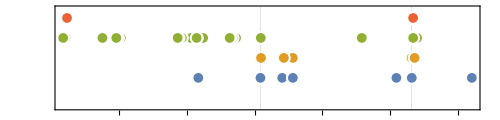

```mathematica
TimelinePlot[extremeDates,PlotLegends->database[[All,"Name"]],GridLines->{importantDates,None}]
```

## Symmetry test around a point

```mathematica
UpperPercentagePointLine[cmin_,cmax_,cl_]:= {{cmin, UpperPercentagePoint[cl]},{cmax,UpperPercentagePoint[cl]}};

PlotSymmetry[market_,returnType_]:= Module[{returns,standardError,tn,upperLineLimit,meanline,meanPlusSe,meanMinusSe,meanFilling,cline,upp,plotData,p, colors},
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
returns = market[returnType];
standardError = StandardDeviation[returns] / Sqrt[Length[returns]];
tn = MeasureTn[returns];
upperLineLimit = Max[tn["TnValues"][[All,2]]];

(* Plot lines *)
meanline=Line[{{Mean[returns],0},{Mean[returns],upperLineLimit/2.5}}];
meanPlusSe = Line[{{Mean[returns]+standardError,0},{Mean[returns]+standardError,upperLineLimit/2.5}}];
meanMinusSe = Line[{{Mean[returns]-standardError,0},{Mean[returns]-standardError,upperLineLimit/2.5}}];
meanFilling = Rectangle[{Mean[returns]-standardError,0},{Mean[returns]+standardError,upperLineLimit/2.5}];
cline = Line[{{MinimalBy[tn["TnValues"],Last][[1,1]],0},{MinimalBy[tn["TnValues"],Last][[1,1]],upperLineLimit/2.5}}];
upp = Map[UpperPercentagePointLine[tn["MinimumC"],tn["MaximumC"],#]&,{0.01,0.05,0.1}];
plotData = Join[{tn["TnValues"]},upp];

p = ListLinePlot[plotData,
PlotTheme->"Monochrome",
FrameLabel->{
Style["c",15],
Style["T_n(c)",13]
},
Epilog->{
meanline,
cline,
meanPlusSe,
meanMinusSe,

{
Gray,
Opacity[0.4],
meanFilling
},

Inset[Text["μ"],{Mean[returns],upperLineLimit/2}],
Inset[Text["μ+SE"],{Mean[returns]+standardError,upperLineLimit/2}],
Inset[Text["μ-SE"],{Mean[returns]-standardError,upperLineLimit/2}],
Inset[Text["C"],{MinimalBy[tn["TnValues"],Last][[1,1]],1.7+upperLineLimit/2}]
},
PlotLegends->Placed[{"T_n","99% CL","95% CL","90% CL"},{Right,Top}], 
PlotLabel->market["Name"],ImageSize->500,Frame->True,BaseStyle->FontSize->13,
TicksStyle->Large,PlotMarkers->None, PlotStyle->colors
];
Return[p];
];
```

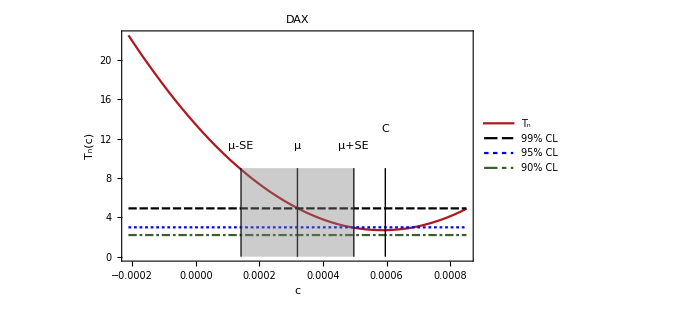
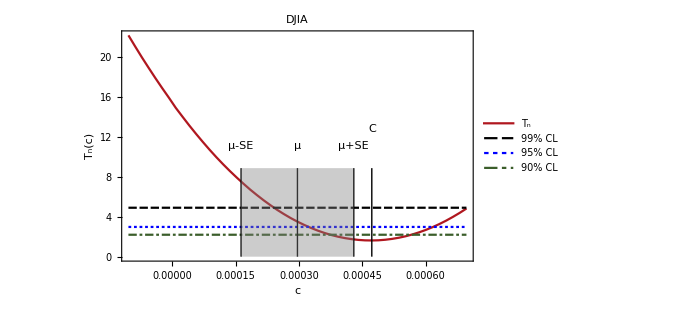
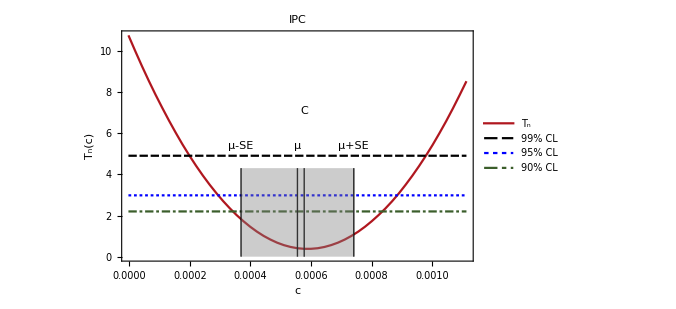
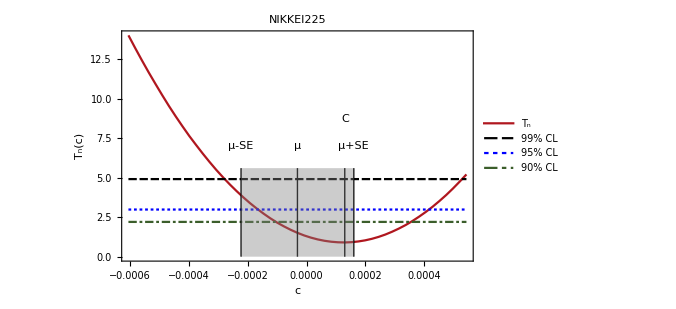

```mathematica
Map[PlotSymmetry[#,"Returns"]&,database]
```